```mathematica
(*
Типовой расчет
Воложинец Архип
221703
Вариант 3
*)
```

```mathematica
data = ({{-0.5, 0.535916}, {-0.42, 0.485126}, {-0.34, 0.437118}, {-0.26, 0.371678}, {-0.18, 0.301733}, {-0.1, 0.207338}, {-0.02, 0.073557}, {0.06, 0.155576}, {0.14, 0.283913}, {0.22, 0.390199}, {0.3, 0.497748}, {0.38, 0.592501}, {0.46, 0.69812}, {0.54, 0.789936}, {0.62, 0.898493}, {0.7, 0.990582}, {0.78, 1.10445}, {0.86, 1.19854}, {0.94, 1.31926}, {1.02, 1.4165}, {1.1, 1.54526}, {1.18, 1.64652}, {1.26, 1.78436}, {1.34, 1.89036}, {1.42, 2.03825}});
```

```mathematica
a = data[[1, 1]];
b = data[[-1, 1]];
h = Abs[a - data[[2, 1]]];
```

```mathematica
(*Аппроксимация функции*)
Q = Fit[data, {1, x, x^2, x^3, x^4, x^5, x^6, x^7, x^8}, x]
```

0.163054+0.123708 x+3.90926 x^2-0.662538 x^3-10.456 x^4+7.54436 x^5+9.26695 x^6-12.0961 x^7+3.60054 x^8

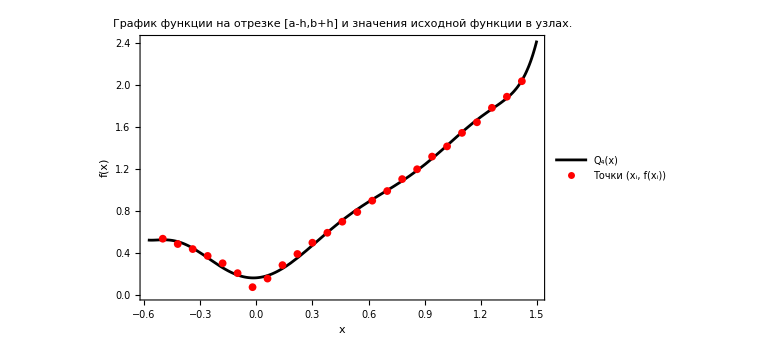

```mathematica
(*График функции на отрезке [a=h,b+h]*)
graph = Plot[Q,{x,a-h,b+h},PlotStyle->Black,PlotLegends->{"Q_4(x)"},ImageSize->Large,AxesLabel->{"x","f(x)"},Frame->True,FrameLabel->{"x","f(x)"},PlotLabel->"График функции на отрезке [a-h,b+h] и значения исходной функции в узлах."];
dots = ListPlot[data,PlotStyle->Red,PlotMarkers->{Automatic,8},PlotLegends->PointLegend[{Red},{"Точки (x_i, f(x_i))"}]];
Show[graph, dots]
```

```mathematica
(*Задание 1*)
```

```mathematica
(*Интерполяционный многочлен степени n = 25*)
```

```mathematica
Subscript[n, 1] = 25;
Subscript[data, 1] = {};
Do[AppendTo[Subscript[data, 1],data[[i]]],{i, Subscript[n, 1]}];
int1 = InterpolatingPolynomial[Subscript[data, 1], x]
```

2.03825+(-1.42+x) (0.782466+(0.5+x) (0.639066+(-0.46+x) (-0.743105+(0.1+x) (0.404103+(-1.1+x) (1.86527+(0.34+x) (-1.82763+(-0.86+x) (1.82974+(-1.34+x) (1.53311+(-0.14+x) (-4.31511+(0.42+x) (4.54101+(-1.26+x) (1.83174+(-0.62+x) (-17.29+(0.26+x) (-9.07332+(-0.3+x) (5.6817+(-1.02+x) (-2140.77+(0.02+x) (2417.52+(-1.18+x) (111.624+(-0.7+x) (-10509.5+(31097.2+(-40463.9+(205603.+(360810.+(223407.+1.94734×10^7 (-0.38+x)) (-0.78+x)) (-0.06+x)) (-0.22+x)) (-0.94+x)) (0.18+x)))))))))))))))))))

```mathematica
(*Интерполяционный многочлен степени n = 12*)
```

```mathematica
Subscript[n, 2] = 12;
Subscript[data, 2] = {};
Do[AppendTo[Subscript[data, 2],data[[2*i + 1]]],{i,0, n/2 -1}];
int2 = InterpolatingPolynomial[Subscript[data, 2], x]
```

1.78436+(-1.26+x) (0.709343+(0.5+x) (0.788597+(-0.3+x) (-0.491973+(-0.78+x) (-0.0519424+(0.18+x) (0.332408+(-1.1+x) (-1.20396+(0.34+x) (0.316969+(-0.62+x) (32.9727+(-33.7292+(130.352-211.257 (-0.14+x)) (-0.94+x)) (0.02+x)))))))))

```mathematica
(*Интерполяционный многочлен степени n = 8*)
```

```mathematica
Subscript[n, 3]= 8;
Subscript[data, 3] = {};
Do[AppendTo[Subscript[data, 3],data[[3*i]]],{i, n / 3}];
int3 = InterpolatingPolynomial[Subscript[data, 3], x]
```

1.89036+(-1.34+x) (0.865025+(0.34+x) (0.676266+(-0.38+x) (-0.408424+(-0.86+x) (0.853461+(-0.635788+(-2.29665+2.53175 (-0.14+x)) (-1.1+x)) (0.1+x)))))

```mathematica
(*Интерполяционный многочлен степени n = 5*)
```

```mathematica
Subscript[n, 4]= 5;
Subscript[data, 4] = {};
Do[AppendTo[Subscript[data, 4],data[[5*i]]],{i, n / 5}];
int4= InterpolatingPolynomial[Subscript[data, 4], x]
```

2.03825+(-1.42+x) (1.08532+(0.424216+(-0.739788+0.820549 (-0.22+x)) (-0.62+x)) (0.18+x))

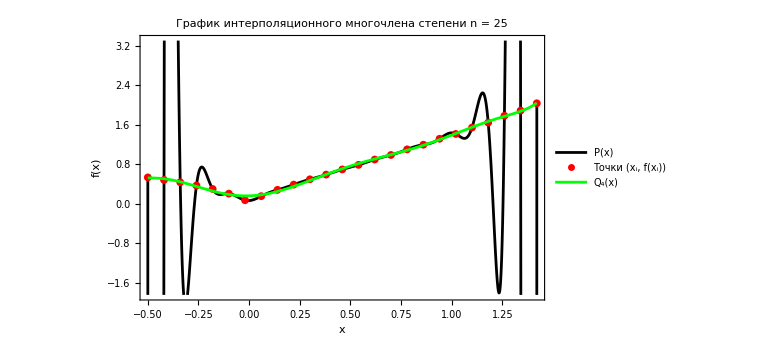

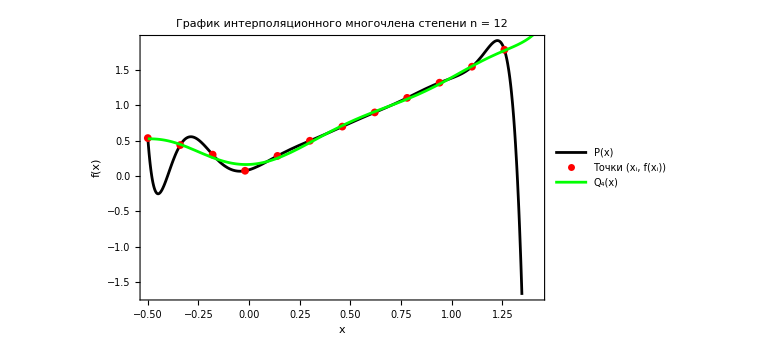

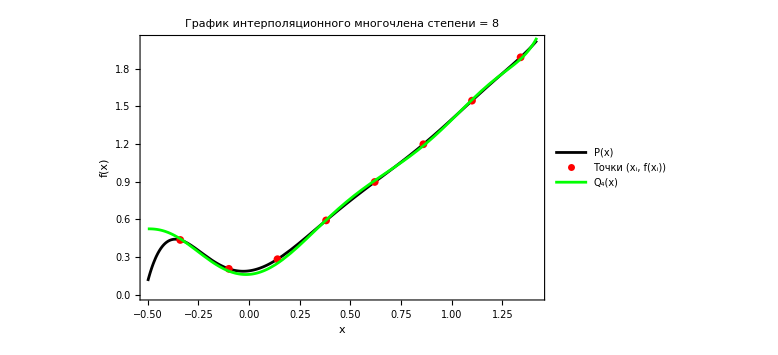

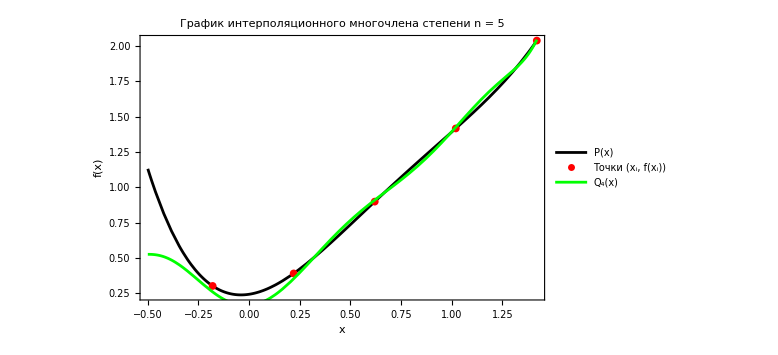

```mathematica
graph1 = Plot[int1,{x,a,b },PlotStyle->Black,PlotLegends->{"P(x)"},ImageSize->Large,AxesLabel->{"x","f(x)"},Frame->True,FrameLabel->{"x","f(x)"},PlotLabel->"График интерполяционного многочлена степени n = 25"];
dots1 = ListPlot[Subscript[data, 1],PlotStyle->Red,PlotMarkers->{Automatic,8},PlotLegends->PointLegend[{Red},{"Точки (x_i, f(x_i))"}]];
graph2 = Plot[int2,{x,a,b},PlotStyle->Black,PlotLegends->{"P(x)"},ImageSize->Large,AxesLabel->{"x","f(x)"},Frame->True,FrameLabel->{"x","f(x)"},PlotLabel->"График интерполяционного многочлена степени n = 12"];
dots2= ListPlot[Subscript[data, 2],PlotStyle->Red,PlotMarkers->{Automatic,8},PlotLegends->PointLegend[{Red},{"Точки (x_i, f(x_i))"}]];
graph3 = Plot[int3,{x,a,b},PlotStyle->Black,PlotLegends->{"P(x)"},ImageSize->Large,AxesLabel->{"x","f(x)"},Frame->True,FrameLabel->{"x","f(x)"},PlotLabel->"График интерполяционного многочлена степени = 8"];
dots3 = ListPlot[Subscript[data, 3],PlotStyle->Red,PlotMarkers->{Automatic,8},PlotLegends->PointLegend[{Red},{"Точки (x_i, f(x_i))"}]];
graph4 = Plot[int4,{x,a,b},PlotStyle->Black,PlotLegends->{"P(x)"},ImageSize->Large,AxesLabel->{"x","f(x)"},Frame->True,FrameLabel->{"x","f(x)"},PlotLabel->"График интерполяционного многочлена степени n = 5"];
dots4 = ListPlot[Subscript[data, 4],PlotStyle->Red,PlotMarkers->{Automatic,8},PlotLegends->PointLegend[{Red},{"Точки (x_i, f(x_i))"}]];
graph = Plot[Q,{x,a,b},PlotStyle->Green,PlotLegends->{"Q_4(x)"},ImageSize->Large,AxesLabel->{"x","f(x)"},Frame->True,FrameLabel->{"x","f(x)"},PlotLabel->"График аппроксимирующей функции
на отрезке [a-h,b+h] и значения исходной функции в узлах."];
Show[graph1, dots1, graph]
Show[graph2, dots2, graph]
Show[graph3,dots3, graph]
Show[graph4, dots4, graph]
```

```mathematica
(*Вывод: исходя из полученного результата с увеличением узлов интерполирования погрешность уменьшается*)
```

```mathematica
(*Задание 2*)
```

```mathematica
Needs["Splines`"];
```

```mathematica
Subscript[n, 1]= 5;
Subscript[data, 1] = {};
Do[AppendTo[Subscript[data, 1],data[[5*i]]],{i, n / 5}];
int1= InterpolatingPolynomial[Subscript[data, 1], x]
```

2.03825+(-1.42+x) (1.08532+(0.424216+(-0.739788+0.820549 (-0.22+x)) (-0.62+x)) (0.18+x))

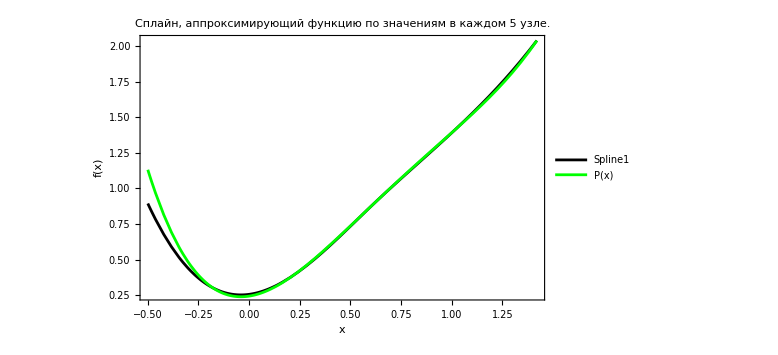

```mathematica
spl1 = Plot[Interpolation[Subscript[data, 1],Method->"Spline"][x],{x,a,b},PlotStyle->Black,PlotLegends->{"Spline1"},ImageSize->Large,AxesLabel->{"x","f(x)"},Frame->True,FrameLabel->{"x","f(x)"},PlotLabel->"Сплайн, аппроксимирующий функцию по значениям в каждом 5 узле."];
graph1 = Plot[int1,{x,a,b },PlotStyle->Green,PlotLegends->{"P(x)"},ImageSize->Large,AxesLabel->{"x","f(x)"},Frame->True,FrameLabel->{"x","f(x)"},PlotLabel->"График интерполяционного многочлена 5 степени."];
Show[spl1, graph1]
```

```mathematica
(*График расходится в начале, в конце расхождение минимально*)
```

```mathematica
Subscript[n, 2]= 8;
Subscript[data, 2] = {};
Do[AppendTo[Subscript[data, 2],data[[3*i]]],{i, n / 3}];
int2 = InterpolatingPolynomial[Subscript[data, 2], x]
```

1.89036+(-1.34+x) (0.865025+(0.34+x) (0.676266+(-0.38+x) (-0.408424+(-0.86+x) (0.853461+(-0.635788+(-2.29665+2.53175 (-0.14+x)) (-1.1+x)) (0.1+x)))))

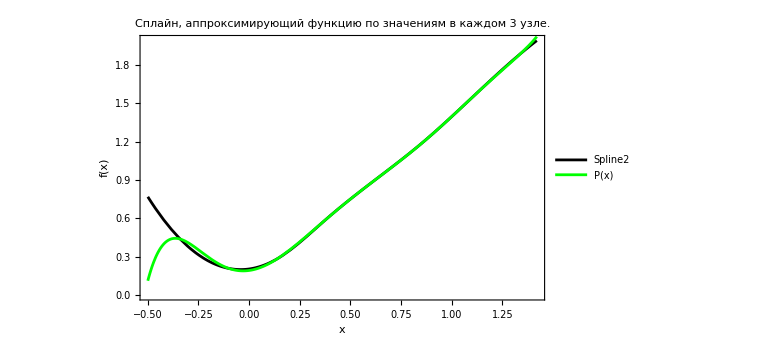

```mathematica
spl2 = Plot[Interpolation[Subscript[data, 2],Method->"Spline"][x],{x,a,b},PlotStyle->Black,PlotLegends->{"Spline2"},ImageSize->Large,AxesLabel->{"x","f(x)"},Frame->True,FrameLabel->{"x","f(x)"},PlotLabel->"Сплайн, аппроксимирующий функцию по значениям в каждом 3 узле."];
graph2 = Plot[int2,{x,a,b },PlotStyle->Green,PlotLegends->{"P(x)"},ImageSize->Large,AxesLabel->{"x","f(x)"},Frame->True,FrameLabel->{"x","f(x)"},PlotLabel->"График интерполяционного многочлена 8 степени."];
Show[spl2, graph2]
```

```mathematica
(*График расходится в начале, в конце расхождение минимально*)
```

```mathematica
Subscript[n, 3] = 12;
Subscript[data, 3] = {};
Do[AppendTo[Subscript[data, 3],data[[2*i + 1]]],{i,0, n/2 -1}];
int3 = InterpolatingPolynomial[Subscript[data, 3], x]
```

1.78436+(-1.26+x) (0.709343+(0.5+x) (0.788597+(-0.3+x) (-0.491973+(-0.78+x) (-0.0519424+(0.18+x) (0.332408+(-1.1+x) (-1.20396+(0.34+x) (0.316969+(-0.62+x) (32.9727+(-33.7292+(130.352-211.257 (-0.14+x)) (-0.94+x)) (0.02+x)))))))))

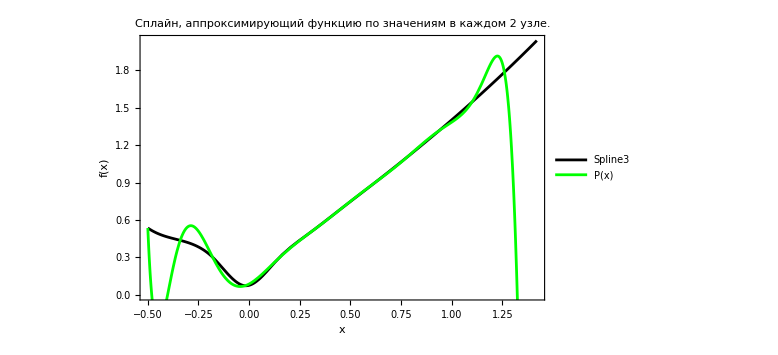

```mathematica
spl3 = Plot[Interpolation[Subscript[data, 3],Method->"Spline"][x],{x,a,b},PlotStyle->Black,PlotLegends->{"Spline3"},ImageSize->Large,AxesLabel->{"x","f(x)"},Frame->True,FrameLabel->{"x","f(x)"},PlotLabel->"Сплайн, аппроксимирующий функцию по значениям в каждом 2 узле."];
graph3 = Plot[int3,{x,a,b },PlotStyle->Green,PlotLegends->{"P(x)"},ImageSize->Large,AxesLabel->{"x","f(x)"},Frame->True,FrameLabel->{"x","f(x)"},PlotLabel->"График интерполяционного многочлена 12 степени."];
Show[spl3, graph3]
```

```mathematica
(*График расходится в начале и конце*)
```

```mathematica
Subscript[n, 4] = 25;
Subscript[data, 4] = {};
Do[AppendTo[Subscript[data, 4],data[[i]]],{i, Subscript[n, 4]}];
int4 = InterpolatingPolynomial[Subscript[data, 4], x]
```

2.03825+(-1.42+x) (0.782466+(0.5+x) (0.639066+(-0.46+x) (-0.743105+(0.1+x) (0.404103+(-1.1+x) (1.86527+(0.34+x) (-1.82763+(-0.86+x) (1.82974+(-1.34+x) (1.53311+(-0.14+x) (-4.31511+(0.42+x) (4.54101+(-1.26+x) (1.83174+(-0.62+x) (-17.29+(0.26+x) (-9.07332+(-0.3+x) (5.6817+(-1.02+x) (-2140.77+(0.02+x) (2417.52+(-1.18+x) (111.624+(-0.7+x) (-10509.5+(31097.2+(-40463.9+(205603.+(360810.+(223407.+1.94734×10^7 (-0.38+x)) (-0.78+x)) (-0.06+x)) (-0.22+x)) (-0.94+x)) (0.18+x)))))))))))))))))))

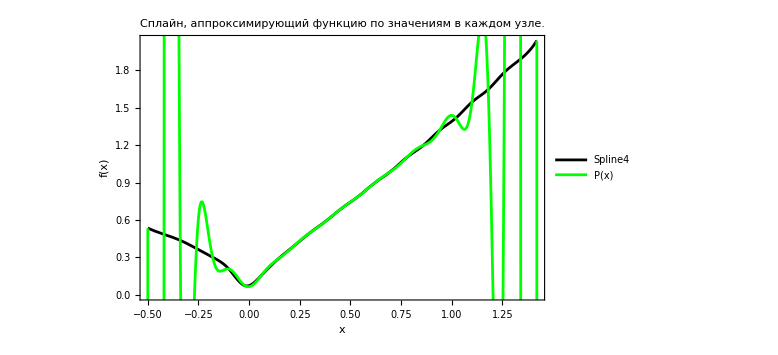

```mathematica
spl4 = Plot[Interpolation[Subscript[data, 4],Method->"Spline"][x],{x,a,b},PlotStyle->Black,PlotLegends->{"Spline4"},ImageSize->Large,AxesLabel->{"x","f(x)"},Frame->True,FrameLabel->{"x","f(x)"},PlotLabel->"Сплайн, аппроксимирующий функцию по значениям в каждом узле."];
graph4 = Plot[int4,{x,a,b },PlotStyle->Green,PlotLegends->{"P(x)"},ImageSize->Large,AxesLabel->{"x","f(x)"},Frame->True,FrameLabel->{"x","f(x)"},PlotLabel->"График интерполяционного многочлена 25 степени."];
Show[spl4, graph4]
```

```mathematica
(*В середние график расходится минимально, в начале и конце сильные расхождения*)
```

```mathematica
(*Вывод: c уменьшением узлов интерполяции достигается максимальное совпадение сплайна с графом*)
```

```mathematica
(*Задание 3*)
```

```mathematica
(*Многочлен наилучшего среднеквадратичного приближения степени n = 1*)
```

0.443208+0.919377 x

1.32923

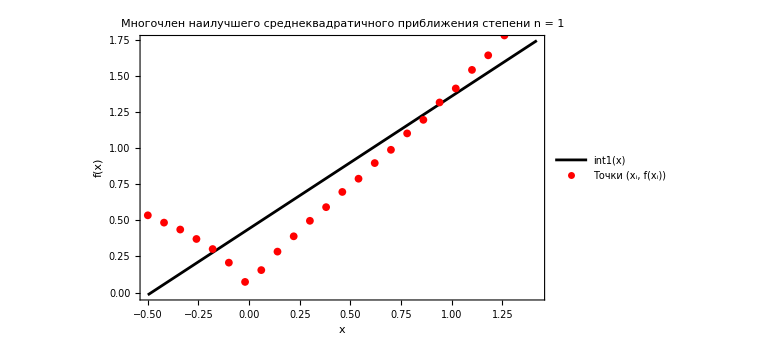

```mathematica
int1 = Fit[data, {1, x}, x]
s1 = ∑_(i=1)^25 (int1 /. x -> data[[i]][[1]] - data[[i]][[2]])^2
graph = Plot[int1,{x,a,b},PlotStyle->Black,PlotLegends->{"int1(x)"},ImageSize->Large,AxesLabel->{"x","f(x)"},Frame->True,FrameLabel->{"x","f(x)"},PlotLabel->"Многочлен наилучшего среднеквадратичного приближения степени n = 1"];
dots = ListPlot[data,PlotStyle->Red,PlotMarkers->{Automatic,8},PlotLegends->PointLegend[{Red},{"Точки (x_i, f(x_i))"}]];
Show[graph, dots]
```

```mathematica
(*Многочлен наилучшего среднеквадратичного приближения степени n = 2*)
```

0.358353+0.275264 x+0.700123 x^2

4.39428

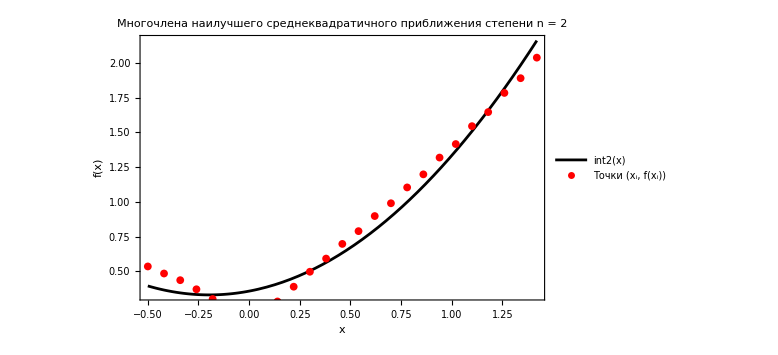

```mathematica
int2 = Fit[data, {1, x, x^2}, x]
s2 = s1 = ∑_(i=1)^25 (int2 /. x -> data[[i]][[1]] - data[[i]][[2]])^2
graph = Plot[int2,{x,a,b},PlotStyle->Black,PlotLegends->{"int2(x)"},ImageSize->Large,AxesLabel->{"x","f(x)"},Frame->True,FrameLabel->{"x","f(x)"},PlotLabel->"Многочлена наилучшего среднеквадратичного приближения степени n = 2"];
dots = ListPlot[data,PlotStyle->Red,PlotMarkers->{Automatic,8},PlotLegends->PointLegend[{Red},{"Точки (x_i, f(x_i))"}]];
Show[graph, dots]
```

```mathematica
(*Задание 4*)
```

```mathematica
a = data[[1, 1]];
b = data[[-1, 1]];
n = 24;
(*Метод левых прямоугольников*)
leftRectangle = (b-a)/n*∑_(i=1)^n data[[i]][[2]]
```

1.56918

```mathematica
(*Метод правых прямоугольников*)
rightRectangle = (b-a)/n*∑_(i=2)^(n+1) data[[i]][[2]]
```

1.68937

```mathematica
(*Метод средних прямоугольников*)
middleRectangle = (b-a)/(n/2)*∑_(i=1)^(n/2) data[[2*i]][[2]]
```

1.62158

```mathematica
(*Метод трапеций*)
trapezoid= (b-a)/n*((data[[1]][[2]])/2+ ∑_(i=2)^n data[[i]][[2]]+(data[[n+1]][[2]])/2)
```

1.62928

```mathematica
(*Метод Симпсона*)
n = 12;
h = (b-a)/(2n);
simpson = h/3∑_(i=1)^n (data[[2i - 1]][[2]] + 4data[[2i]][[2]] + data[[2i+1]][[2]])
```

1.62671

```mathematica
(*Выведем значение интеграла апроксимированной функции для сравнения*)
Q = Fit[data, {1, x, x^2, x^3, x^4, x^5, x^6, x^7, x^8}, x]
Integrate[Q, {x, a, b}]
```

0.163054+0.123708 x+3.90926 x^2-0.662538 x^3-10.456 x^4+7.54436 x^5+9.26695 x^6-12.0961 x^7+3.60054 x^8

1.62786

```mathematica
(*Вывод: максимально точными способами оказались методы Симпосна и трапеций*)
```

```mathematica
(*Задание 5*)
```

```mathematica
Subscript[n, 4]= 5;
Subscript[data, 4] = {};
Do[AppendTo[Subscript[data, 4],data[[5*i]]],{i, n / 5}];
int4= InterpolatingPolynomial[Subscript[data, 4], x]
n = 25;
h = (b-a)/(n-1);
firstPrecisionTableD1 = Table[(data[[i+1]][[2]] -data[[i]][[2]])/h, {i, 1, n-1}];
secondPrecisionTableD1 = Prepend[Table[(data[[i+1]][[2]] -data[[i-1]][[2]])/(2h), {i, 2, n-1}], "-"];
tableOfFirstDerivative = {};
AppendTo[tableOfFirstDerivative, {"x", "f'(x) 1-го порядка точности", "f'(x) 2-го порядка точности", "Функция D апроксимируемой функции"}];
i = 1;
While[i <= n,If[i > n-1, AppendTo[tableOfFirstDerivative, {data[[i]][[1]],"-", "-", D[int4, x] /. x-> data[[i]][[1]]}], AppendTo[tableOfFirstDerivative, {data[[i]][[1]],firstPrecisionTableD1[[i]], secondPrecisionTableD1[[i]], D[Q, x] /. x-> data[[i]][[1]]}]] ; i++];
Grid[tableOfFirstDerivative, {Dividers->All,Spacings->1.5 {1,1}}]
```

0.390199+0.221165 (-0.22+x)

x | f'(x) 1-го порядка точности | f'(x) 2-го порядка точности | Функция D апроксимируемой функции
-0.5 | -0.634875 | - | 0.017553
-0.42 | -0.6001 | -0.617487 | -0.496086
-0.34 | -0.818 | -0.70905 | -1.01498
-0.26 | -0.874313 | -0.846156 | -1.23052
-0.18 | -1.17994 | -1.02713 | -1.07807
-0.1 | -1.67226 | -1.4261 | -0.633067
-0.02 | 1.02524 | -0.323513 | -0.0331172
0.06 | 1.60421 | 1.31473 | 0.577157
0.14 | 1.32858 | 1.46639 | 1.08145
0.22 | 1.34436 | 1.33647 | 1.41038
0.3 | 1.18441 | 1.26439 | 1.54636
0.38 | 1.32024 | 1.25232 | 1.51789
0.46 | 1.1477 | 1.23397 | 1.38616
0.54 | 1.35696 | 1.25233 | 1.22711
0.62 | 1.15111 | 1.25404 | 1.11203
0.7 | 1.42335 | 1.28723 | 1.0896
0.78 | 1.17613 | 1.29974 | 1.17254
0.86 | 1.509 | 1.34256 | 1.33187
0.94 | 1.2155 | 1.36225 | 1.50186
1.02 | 1.6095 | 1.4125 | 1.59859
1.1 | 1.26575 | 1.43762 | 1.55536
1.18 | 1.723 | 1.49437 | 1.37783
1.26 | 1.325 | 1.524 | 1.22204
1.34 | 1.84863 | 1.58681 | 1.49826
1.42 | - | - | 0.221165

```mathematica
(*Вывод: формулы второго порядка точности оказались более приближенными*)
```

```mathematica
firstPrecisionTableD2 = Append[Table[(firstPrecisionTableD1[[i+1]] -firstPrecisionTableD1[[i]])/h, {i, 1, n-2}], "-"];
secondPrecisionTableD2 = Prepend[Table[(data[[i+1]][[2]]-2data[[i]][[2]]+data[[i-1]][[2]])/h^2, {i, 2, n-1}], "-"];
tableOfSecondDerivative = {};
AppendTo[tableOfSecondDerivative, {"x", "f''(x) 1-го порядка точности", "f''(x) 2-го порядка точности", "Функция D апроксимируемой функции"}];
i = 1;
While[i <= n,If[i < n, AppendTo[tableOfSecondDerivative, {data[[i]][[1]],firstPrecisionTableD2[[i]], secondPrecisionTableD2[[i]], D[Q, {x, 2}] /. x-> data[[i]][[1]]}], AppendTo[tableOfSecondDerivative, {data[[i]][[1]],"-", "-", D[int4, {x, 2}] /. x-> data[[i]][[1]]}]]; i++];
Grid[tableOfSecondDerivative, {Dividers->All,Spacings->1.5 {1,1}}]
```

x | f''(x) 1-го порядка точности | f''(x) 2-го порядка точности | Функция D апроксимируемой функции
-0.5 | 0.434687 | - | -4.02058
-0.42 | -2.72375 | 0.434687 | -7.42692
-0.34 | -0.703906 | -2.72375 | -4.93003
-0.26 | -3.82031 | -0.703906 | -0.345478
-0.18 | -6.15406 | -3.82031 | 3.98349
-0.1 | 33.7188 | -6.15406 | 6.84351
-0.02 | 7.23719 | 33.7188 | 7.84667
0.06 | -3.44547 | 7.23719 | 7.16411
0.14 | 0.197344 | -3.44547 | 5.29776
0.22 | -1.99937 | 0.197344 | 2.89007
0.3 | 1.69781 | -1.99937 | 0.571767
0.38 | -2.15672 | 1.69781 | -1.1522
0.46 | 2.61578 | -2.15672 | -1.97883
0.54 | -2.57313 | 2.61578 | -1.84504
0.62 | 3.40297 | -2.57313 | -0.927657
0.7 | -3.09031 | 3.40297 | 0.394647
0.78 | 4.16094 | -3.09031 | 1.61753
0.86 | -3.66875 | 4.16094 | 2.22515
0.94 | 4.925 | -3.66875 | 1.84244
1.02 | -4.29688 | 4.925 | 0.425394
1.1 | 5.71563 | -4.29688 | -1.51054
1.18 | -4.975 | 5.71563 | -2.62406
1.26 | 6.54531 | -4.975 | -0.443509
1.34 | - | 6.54531 | 8.97563
1.42 | - | - | 0.

```mathematica
(*Вывод: расхождения слишком велики, чтобы делать конкретный вывод*)
```